# Exam 2 -- Carter Colton

```mathematica
SetDirectory[NotebookDirectory[]] 
Clear["`*" ]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica

## Problem 1

Alice, Bob, Joe, and Sally have a combined age of 100 years.  The boys combined ages are the same as the girls combined ages.  Ten years from now, Joe will be twice as old as Alice, i.e., Joe’s age in ten years will be twice Alice’s age in ten years.  In twenty years, Bob will be as old as Sally is now.

Find the ages of Alice, Bob, Joe, and Sally using Mathematic’s LinearSolve function.

a+b+j+s = 100
b+j = a+s
j+10 = 2(a+10)
b+20 = s

```mathematica
Testmatrix={{1,1,1,1},{-1,1,1,-1},{-2,0,1,0},{0,1,0,-1}};
Testmatrix//MatrixForm
```

(1 | 1 | 1 | 1
-1 | 1 | 1 | -1
-2 | 0 | 1 | 0
0 | 1 | 0 | -1)

```mathematica
solutionstestmatrix={100,0,10,-20};
solutionstestmatrix//MatrixForm
```

(100
0
10
-20)

```mathematica
LinearSolve[Testmatrix,solutionstestmatrix];
%//MatrixForm//N
```

(10.
20.
30.
40.)

## Problem 2

Create an animated gif that depicts this function from times of t = 0 to t = 10, using time steps of 0.1:  f(x, t) = ∑_(k=1)^10 e^(-(k-5)^2/6)Cos[k x +k^1.2 t].  Plot the x-axis from -5 to 5 and fix the y-axis plot range to be -5 to 5. Call the output file “p2output-[yourlastname].gif” and it should output the file into the same directory as your exam solutions notebook.

```mathematica
Clear[x,t]
```

```mathematica
f[x_,t_]=Sum[E^(-(i-5)^2/6)*Cos[i*x+i^1.2*t],{i,1,10}]
```

Cos[1. t+x]/ⅇ^(8/3)+Cos[2.2974 t+2 x]/ⅇ^(3/2)+Cos[3.73719 t+3 x]/ⅇ^(2/3)+Cos[5.27803 t+4 x]/ⅇ^(1/6)+Cos[6.89865 t+5 x]+Cos[8.58581 t+6 x]/ⅇ^(1/6)+Cos[10.3304 t+7 x]/ⅇ^(2/3)+Cos[12.1257 t+8 x]/ⅇ^(3/2)+Cos[13.9666 t+9 x]/ⅇ^(8/3)+Cos[15.8489 t+10 x]/ⅇ^(25/6)

```mathematica
table = Table[Plot[f[x,t],{x,-5,5},PlotRange->{All,{-5,5}},PlotPoints->50],{t,0,10,0.1}];
```

```mathematica
Export["p2output-[Colton].gif",table,AnimationRate->10]
```

p2output-[Colton].gif

## Problem 3

Use Module to create a function which returns the Least Common Multiple (LCM) of two integers. Of course, Mathematica has a built-in function to do this, but I want you to write your own--call it myLCM.  There are many possible ways to do this, but DO NOT use the built-in function LCM.  Test your function for the numbers (12, 16) that should return myLCM[12,16] = 48 and for the numbers (21,99) that should return myLCM[21, 99] = 693.

Hint: I used the Mathematica function IntegerQ, but I am sure there are other ways to solve this problem.

```mathematica
myLCM[integer1_,integer2_]:=Module[{},
fraction=(Simplify[integer1/integer2]);
Numerator[fraction]*integer2
]
```

```mathematica
myLCM[12,16]
```

48

```mathematica
myLCM[21,99]
```

693

```mathematica
myLCM[2,3]
```

6

```mathematica
myLCM[132,66]
```

132

## Problem 4

Consider the transcendental equation x^2=exp(x) cos(x). As the Plot command below shows, it has two solutions (the left and right hand sides of the equation intersect in two spots), one near x = -0.5 and one that looks to me like it’s around x = 1.2. Find the second solution via iterative computation. Do this by recognizing that the solution to that equation is the same as the solution to this equation (square rooting both sides): x = sqrt(exp(x) cos(x)), so if you iteratively compute sqrt(exp(x) cos(x)) and it converges to an answer, that is the solution.

As was done in one of the lab assignments from the Programming I lab, I’d like you to do this using a While loop. (This can be outside of a Module.) Start with a global variable, latest = 1.2, and use While to recursively compute sqrt(exp(x) cos(x)) until the magnitude of the change between recursions is less than 10^-7. In other words, keep evaluating  latest = sqrt (exp(latest) cos(latest))   as long as abs(sqrt(exp(latest) cos(latest))  -  latest) > 10^-7.  Use a second global variable to count the number of iterations the loop goes through before the 10^-7 tolerance is reached. Display the answer along with the number of iterations. 

You can use FindRoot to check your answer if you’d like.

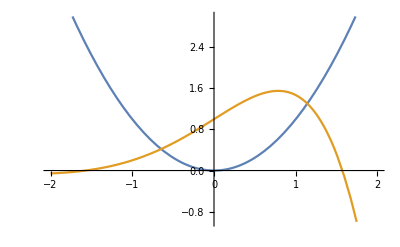

```mathematica
Plot[{x^2,Exp[x]Cos[x]},{x,-2,2}, PlotRange->{-1,3}]
```

```mathematica
latest=1.2;n=0;
While[Abs[Sqrt[Exp[latest]*Cos[latest]]-latest]  > 10^-7,latest=Sqrt[Exp[latest]*Cos[latest]];n++];
latest
n
```

1.1416

36

```mathematica
FindRoot[x^2==Exp[x]*Cos[x],{x,1.2}]
```

{x→1.1416}

```mathematica
x/.%
```

1.1416

## Problem 5

The file exam2p5.csv contains four columns of data.  Let’s call the columns x, y, z, and w.  Write some Mathematica code that imports the data (assuming that the data file is in the same folder as your Mathematica notebook), manipulates it, and exports a new csv file with two data columns whose values are x and z*w + y/10, meaning the new second column values are the product of the z and w values plus one-tenth the y values for a given x value. Call the output file “p5output-[yourlastname].csv”, and it should output the file into the same directory as your exam solutions notebook.

Hint: if you’d like to, you can ListPlot your data. It should look something like exp(-x/10)*cos(x) with some added noise.

```mathematica
data=Import["exam2p5.csv"];
```

```mathematica
newdata={#[[1]]&/@data,#[[3]]*#[[4]]+(#[[2]])/10&/@data};
```

```mathematica
newdatatranspose=Transpose[newdata]
```

{{0,0.979364},{0.1,1.00391},{0.2,1.09112},{0.3,0.972241},{0.4,0.681967},{0.5,0.82246},{0.6,0.594571},{0.7,0.800704},{0.8,0.62227},{0.9,0.565119},{1,0.520859},{1.1,0.371508},{1.2,0.176898},{1.3,0.151281},{1.4,0.0219758},{1.5,0.0894437},{1.6,0.0350657},{1.7,-0.0701467},{1.8,-0.195994},{1.9,-0.320169},{2,-0.323274},{2.1,-0.321508},{2.2,-0.235679},{2.3,-0.405873},{2.4,-0.406822},{2.5,-0.5768},{2.6,-0.429832},{2.7,-0.389771},{2.8,-0.576302},{2.9,-0.71429},{3,-0.514048},{3.1,-0.487773},{3.2,-0.47834},{3.3,-0.298416},{3.4,-0.381511},{3.5,-0.463669},{3.6,-0.555467},{3.7,-0.320733},{3.8,-0.514541},{3.9,-0.318989},{4,-0.421966},{4.1,-0.46573},{4.2,-0.19718},{4.3,-0.320151},{4.4,-0.168572},{4.5,-0.0445295},{4.6,-0.164964},{4.7,0.00495084},{4.8,0.0288293},{4.9,0.0172366},{5,-0.0921768},{5.1,0.048507},{5.2,0.210856},{5.3,0.10878},{5.4,0.357776},{5.5,0.243005},{5.6,0.290958},{5.7,0.29952},{5.8,0.293558},{5.9,0.174443},{6,0.167855},{6.1,0.300751},{6.2,0.393229},{6.3,0.401136},{6.4,0.437484},{6.5,0.324848},{6.6,0.387237},{6.7,0.46853},{6.8,0.346955},{6.9,0.318224},{7,0.0861578},{7.1,0.165979},{7.2,0.00604898},{7.3,0.00871},{7.4,0.0301515},{7.5,0.0663127},{7.6,-0.0451514},{7.7,0.0680925},{7.8,0.125859},{7.9,0.0498915},{8,-0.0290106},{8.1,-0.0776404},{8.2,-0.221767},{8.3,0.0188693},{8.4,0.0236421},{8.5,-0.208413},{8.6,-0.0568323},{8.7,-0.178876},{8.8,0.0800466},{8.9,0.0587297},{9,-0.0956254},{9.1,-0.257663},{9.2,-0.179502},{9.3,-0.19819},{9.4,-0.134548},{9.5,-0.284169},{9.6,-0.247415},{9.7,-0.0138604},{9.8,-0.0398101},{9.9,-0.184615},{10,-0.103671}}

```mathematica
Export["p5output-[Colton].csv",newdatatranspose]
```

p5output-[Colton].csv

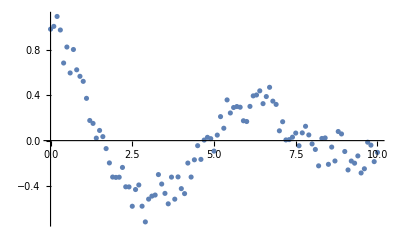

```mathematica
ListPlot[newdatatranspose]
```

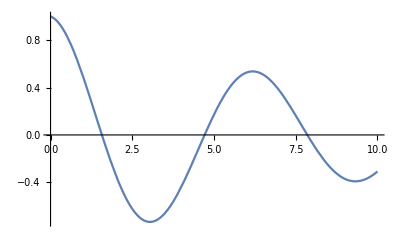

```mathematica
Plot[Exp[-x/10]*Cos[x],{x,0,10}]
```

## Problem 6

Use Module to create a function named “allDivisible” that has two integer argument.  The function should return true if all of the digits of the first number are divisible by the second number and false otherwise.  For example, allDivisible[936, 3] would return True becuase 9, 3, and 6 are each divisible by 3 while allDivisible[936,2] would return False because 3 is not divisible by 2.  Test your function on the following cases:
allDivisible[936,3]
allDivisible[1024, 2]
allDivisible[48404, 4]

Hint: the built-in functions IntegerDigits will be useful. I also used MemberQ in my own solution but I’m sure there are many other ways to do it without using that function.

```mathematica
allDivisible[integer16_,integer26_]:=Module[{},
sizeofnumber=IntegerLength[integer16];
truelist={True};
n=1;While[n<sizeofnumber,AppendTo[truelist,True];n++];
testint=IntegerDigits[integer16];
testlist=#/integer26&/@testint;
If[IntegerQ[#]&/@testlist==truelist,True,False]
]
```

```mathematica
(*I am assuming that 0 is divisible by anything because anything divided by 0 is 0 and 0 is an integer*)
```

```mathematica
allDivisible[936,2]
```

False

```mathematica
allDivisible[936,3]
```

True

```mathematica
allDivisible[1024,2]
```

False

```mathematica
allDivisible[48404,4]
```

True

```mathematica
allDivisible[22222244444488888,2]
```

True

```mathematica
allDivisible[36,3]
```

True

```mathematica
allDivisible[36,2]
```

False

## Problem 7

Use the eigenvalue method to solve for the normal mode frequencies for two coupled masses with unequal masses (m1 = 1 and m2 = 2, listed from left to right) and unequal spring constants (k1 = 4, k2 = 5, and k3 = 6, listed from left to right).  Use the eigenvectors to describe the motion for the two normal modes, being clear which motion corresponds to which frequency. 
  
I’ll set you up with the equations like I did in the lab... using the same techniques as done in the Linear Algebra lab, the equations for the situation of unequal masses and unequal springs become  the following:

m_1(d^2 u)/dt^2=k_2(v-u)-k_1 u
m_2(d^2 v)/dt^2=-k_3v-k_2(v-u)



m_1(d^2 u)/dt^2=u(-k_1-k_2) + v(k_2)
m_2(d^2 v)/dt^2=u(k_2)+v(-k_2-k_3)


m_1 ω^2 u_0=u_0(k_1+k_2) + v_0(-k_2)
m_2 ω^2 v_0=u_0(-k_2)         +v_0(k_2+k_3)


ω^2 u_0=u_0(k_1+k_2)/m_1+ v_0(-k_2/m_1)
ω^2 v_0=u_0(-k_2/m_2)         +v_0(k_2+k_3)/m_2


Or, in matrix form, with λ= ω^2: 

λ(u_0

v_0) = ((k_1+k_2)/m_1 | -k_2/m_1
-k_2/m_2 | (k_2+k_3)/m_2)(u_0

v_0)

Note that I needed to divide the two equations by m1 and m2 respectively in order for the matrix equation to have the proper form for an eigenvalue equation, so λ has a slightly different meaning here than in the lab (where it was  λ= m ω^2).

```mathematica
uandv={u0,v0};
uandv//MatrixForm
```

(u0
v0)

```mathematica
k1=4;
k2=5;
k3=6;
m1=1;
m2=2;
```

```mathematica
kmatrix={{(k1+k2)/m1,-k2/m1},{-k2/m2,(k2+k3)/m2}};
%//MatrixForm
```

(9 | -5
-5/2 | 11/2)

```mathematica
rightside=kmatrix.uandv;
rightside//MatrixForm
```

(9 u0-5 v0
-(5 u0)/2+(11 v0)/2)

```mathematica
Eigenvectors[kmatrix]
%//MatrixForm
```

{{1/10 (-7-√249),1},{1/10 (-7+√249),1}}

(1/10 (-7-√249) | 1
1/10 (-7+√249) | 1)

```mathematica
Eigenvalues[kmatrix]
```

{1/4 (29+√249),1/4 (29-√249)}

lamda = omega^2
Two allowed values for the frequency are Sqrt[1/4(29+√249)] and Sqrt[1/4 (29-√249)]

```mathematica
Eigensystem[kmatrix]
```

{{1/4 (29+√249),1/4 (29-√249)},{{1/10 (-7-√249),1},{1/10 (-7+√249),1}}}

The allowed frequency of Sqrt[1/4(29+√249)] has u0 at 1/10 (-7-√249) and v0 at 1 while the 
allowed frequency at Sqrt[1/4 (29-√249)] has u0 at 1/10 (-7+√249) and v0 at 1

```mathematica
(*remember that u0 and v0 describe the motion and the Sqrt[eigenvalues]/allowed frequencies the frequency. The u0 and v0 described directly above are the eigenvectors and the allowed frequencies are their corresponding eigenvalues*)
```

## Problem 8

The file exam2p8.csv contains two columns of experimental data.  Fit the data to a Gaussian peak, which is related to the Normal Distribution, of the form: f(x) = y_0  +  A/(w sqrt(π/2))exp(-(2 (x-x_0)^2)/w^2) , where x_0, w, y_0, and A are fitting parameters corresponding to the peak center, peak width, y-offset, and peak area (as measured from the y-offset), respectively. For each of the four parameters report their best fit values and their uncertainties (you don’t have to create any special output here, just make sure those eight values are all output in some form).  As in problem 5, write your Mathematica code assuming that the data file is in the same folder as your Mathematica notebook.


Hint: if you’d like to, you can Plot your fit on top of a ListPlot of the data. They should overlap nicely.

Another hint: if you used “x” and “w” as a variable name above, you might need to Clear them.

```mathematica
Clear[x,w]
```

```mathematica
exam8data=Import["exam2p8.csv"];
```

```mathematica
fitthefunction =y0+A/(w*Sqrt[Pi/2])*E^(-(2*(x-x0)^2)/w^2);
fitresults =FindFit[exam8data,fitthefunction,{x0,w,y0,A},x]
bestx0 = x0/.fitresults[[1]]
bestw =w/.fitresults[[2]]
besty0=y0/.fitresults[[3]]
bestA=A/.fitresults[[4]]
```

{x0→4.70581,w→-1.40269,y0→1.00112,A→-8.28613}

4.70581

-1.40269

1.00112

-8.28613

```mathematica
(*I do not know what it means by finding their uncertainties, so I will just find the absolute value error*)
```

```mathematica
xvals =(exam8data //Transpose) [[1]];  
yvals =(exam8data //Transpose )[[2]];
```

```mathematica
trialabs[x_,x0_,w_,y0_,A_] = fitthefunction ;
yvalstrialabs[x0_,w_,y0_,A_] := Table[trialabs[x,x0,w,y0,A],{x,xvals}];
absError[x0_,w_,y0_,A_] := Total[ Abs[yvals - yvalstrialabs[x0,w,y0,A]]];
absError[bestx0,bestw,besty0,bestA]
```

8.37818

```mathematica
minimumabs=FindMinimum[absError[x0,w,y0,A],{x0,w,y0,A},Method->"PrincipalAxis"]
```

{78.2389,{x0→-0.801559,w→3.95303,y0→1.73773,A→-7.4814}}

## Problem 9

The complex function f = (5 z^3-3 z^2+2)/((z - 3 + 3i)(z - 2i)(z + 3))has three poles in the complex plane: z = 3 - 3i, z = 2i and z = -3.  (Notice these are just the places where the denominator is zero).  If you plug in any of those three numbers, f(z) becomes infinite.  Use the Residue theorem to evaluate a path integral that is centered at z = 0 and makes a circular path of radius 4.

Hint: In Lab 11 you saw that the integral of a closed loop in the complex plane was equal to 2πi times the sum of the residues of any poles enclosed in the loop.  Make sure you only include the residues at the poles that are contained inside the loop.

```mathematica
g[z_] = (5*z^3-3*z^2+2)/((z-3+3*I)*(z-2*I)*(z+3));
gplot=Plot3D[Abs[g[x+I y]],{x,-5,5},{y,-5,5},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True]
```

-Graphics3D-

```mathematica
Solve[(z-3+3*I)*(z-2*I)*(z+3)==0](*Check to see if equation has correct poles*)
%[[1]];
z/.%;
g[%](*Check to see if it does become infinite at one of the poles*)
```

{{z→-3},{z→2 ⅈ},{z→3-3 ⅈ}}

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
z0 = 0;  r= 4;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-5,5},{y,-5,5},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ];
Integrate[integrand ,{θ,0,2Pi}]
```

-Graphics3D-

(-230/51-(814 ⅈ)/51) π

## Problem 10

Consider the function f(z) = sin(z), where z is a complex number. You studied this function in the complex numbers lab.  When z is purely real, z = x, it’s a normal sine function. When z is purely imaginary, z = iy, the imaginary component of the function is equal to sinh(y), and the real component is zero. But what does the function look like when z = a number with equal real and imaginary parts, i.e. along the line y=x in the complex plane such as shown here?  
-Graphics-

Make a plot of the sine function along this line, from the point (-5,-5), i.e. -5 - 5i,  to the point (5,5), i.e. 5 + 5i. Because f12(z) is a complex function you’ll need to plot the real and imaginary parts separately. Or you can plot them on the same graph, if you’d like.

Because you can only use Plot with a real number variable, the x-axis of your plot will need to be some real number parameter that causes the left hand end of your plot to represent the point (-5,-5) and the right hand end of your plot to represent the point (5,5). Probably the easiest way to do that is to use the x-coordinate (i.e. the real value) of z as your plot’s x-axis. I.e. since y always equals x along this line, you can plug z into your function as z = x + i x  where x is always a real number.

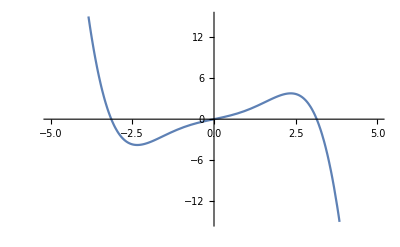

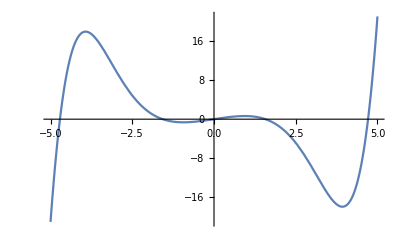

```mathematica
Plot[Re[Sin[x+I*x]],{x,-5,5}]
Plot[Im[Sin[x+I*x]],{x,-5,5}]
```